```mathematica
((x-1)(x-2)/((0-1)(0-2)))*(-1)+(((x-0)(x-2)/((1-0)(1-2))))*0.765789+((((x-0)(x-1))/(2-0)(2-1)))*(-10.263813)
```

-1/2 (-2+x) (-1+x)+0.765789 (2-x) x-5.13191 (-1+x) x

```mathematica
Expand[-1/2 (-2+x) (-1+x)]
```

-1+(3 x)/2-x^2/2

```mathematica
Simplify[-1/2 (-2+x) (-1+x)+0.765789 (2-x) x-5.1319065 (-1+x) x]
```

-1.+8.16348 x-6.3977 x^2

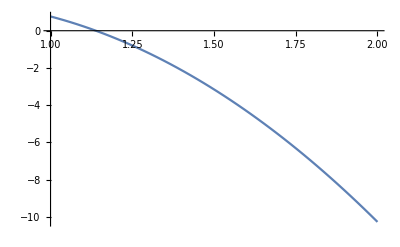

```mathematica
p2=Plot[-1.+8.163484500000001 x-6.3976955 x^2,{x,1,2}]
```

```mathematica
f[x_]:=-1.+8.163484500000001 x-6.3976955 x^2
```

```mathematica
f[1]
```

0.765789

```mathematica
NumberForm[0.7657890000000007,16]
```

0.7657890000000007

```mathematica
f[2]
```

-10.2638

```mathematica
NumberForm[-10.263812999999999,16]
```

-10.263813

```mathematica
f[0]
```

-1.

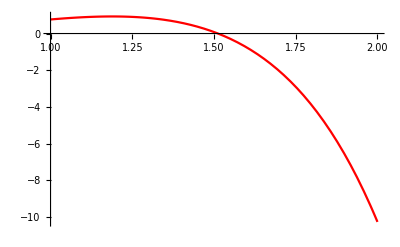

```mathematica
p1=Plot[3x*E^x-E^(2x),{x,1,2},PlotStyle->Red]
```

```mathematica
g[x_]:=3x*E^x-E^(2x)
```

```mathematica
g[1]
```

3 ⅇ-ⅇ^2

```mathematica
N[3 ⅇ-ⅇ^2]
```

0.765789

```mathematica
g[2]
```

6 ⅇ^2-ⅇ^4

```mathematica
N[6 ⅇ^2-ⅇ^4]
```

-10.2638

```mathematica
D[3x*E^x-E^(2x)]
```

-ⅇ^(2 x)+3 ⅇ^x x

```mathematica
D[(-ⅇ^(2 x)+3 ⅇ^x x), x]
```

```mathematica
kl[x_]:=3 ⅇ^x-2 ⅇ^(2 x)+3 ⅇ^x x
```

```mathematica
kl[1]
```

6 ⅇ-2 ⅇ^2

```mathematica
N[6 ⅇ-2 ⅇ^2]
```

1.53158

```mathematica
kl[2]
```

9 ⅇ^2-2 ⅇ^4

```mathematica
N[9 ⅇ^2-2 ⅇ^4]
```

-42.6948

```mathematica
NumberForm[-42.69479517591262,16]
```

-42.69479517591262

```mathematica
N[9 ⅇ^2-2 ⅇ^4]
```

-42.6948

```mathematica
A1[x_]:=(1-2(x-1)*(-1))*(-x+2)^2
```

```mathematica
Simplify[(1+2 (-1+x)) (2-x)^2]
```

(-2+x)^2 (-1+2 x)

```mathematica
Expand[(-2+x)^2 (-1+2 x)]
```

-4+12 x-9 x^2+2 x^3

```mathematica
A2[x_]:=(1-2(x-2))(x-1)^2
```

```mathematica
B1[x_]:=(x-1)(-x+2)^2
```

```mathematica
B2[x_]:=(x-2)(x-1)^2
```

```mathematica
H[x_]:=A1[x]*g[1]+A2[x]*g[2]+B1[x]*kl[1]+B2[x]*kl[2]
```

```mathematica
H[x]
```

(3 ⅇ-ⅇ^2) (1+2 (-1+x)) (2-x)^2+(6 ⅇ-2 ⅇ^2) (2-x)^2 (-1+x)+(6 ⅇ^2-ⅇ^4) (1-2 (-2+x)) (-1+x)^2+(9 ⅇ^2-2 ⅇ^4) (-2+x) (-1+x)^2

```mathematica
Simplify[(3 ⅇ-ⅇ^2) (1+2 (-1+x)) (2-x)^2+(6 ⅇ-2 ⅇ^2) (2-x)^2 (-1+x)+(6 ⅇ^2-ⅇ^4) (1-2 (-2+x)) (-1+x)^2+(9 ⅇ^2-2 ⅇ^4) (-2+x) (-1+x)^2]
```

-ⅇ (ⅇ^3 (-1+x)^2-3 (-2+x)^2 (-3+4 x)+ⅇ (-24+55 x-37 x^2+7 x^3))

```mathematica
Expand[-ⅇ (ⅇ^3 (-1+x)^2-3 (-2+x)^2 (-3+4 x)+ⅇ (-24+55 x-37 x^2+7 x^3))]
```

-36 ⅇ+24 ⅇ^2-ⅇ^4+84 ⅇ x-55 ⅇ^2 x+2 ⅇ^4 x-57 ⅇ x^2+37 ⅇ^2 x^2-ⅇ^4 x^2+12 ⅇ x^3-7 ⅇ^2 x^3

```mathematica
Factor[-36 ⅇ+24 ⅇ^2-ⅇ^4+84 ⅇ x-55 ⅇ^2 x+2 ⅇ^4 x-57 ⅇ x^2+37 ⅇ^2 x^2-ⅇ^4 x^2+12 ⅇ x^3-7 ⅇ^2 x^3]
```

-ⅇ (36-24 ⅇ+ⅇ^3-84 x+55 ⅇ x-2 ⅇ^3 x+57 x^2-37 ⅇ x^2+ⅇ^3 x^2-12 x^3+7 ⅇ x^3)

```mathematica
N[%]
```

-2.71828 (-9.15323+25.3344 x-23.4909 x^2+7.02797 x^3)

```mathematica
Simplify[-2.718281828459045 (-9.153226959829418+25.334426718872137 x-23.490890729797 x^2+7.027972799213316 x^3)]
```

24.8811-68.8661 x+63.8549 x^2-19.104 x^3

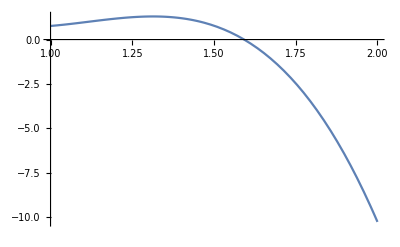

```mathematica
Plot[24.881050516665738-68.86611178433743 x+63.854861405124225 x^2-19.104010751006005 x^3,{x,1,2}]
```

```mathematica
H[1]
```

3 ⅇ-ⅇ^2

```mathematica
N[3 ⅇ-ⅇ^2]
```

0.765789

```mathematica
H[2]
```

6 ⅇ^2-ⅇ^4

```mathematica
N[6 ⅇ^2-ⅇ^4]
```

-10.2638

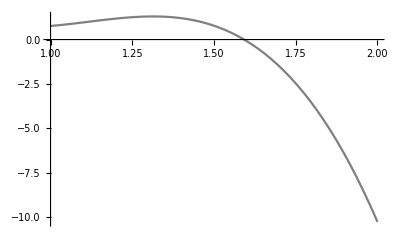

```mathematica
p3=Plot[H[x],{x,1,2},PlotStyle->Gray]
```

```mathematica
g[1.2]
```

0.929245

```mathematica
f[1.2]
```

-0.4165

```mathematica
H[1.2]
```

1.18099

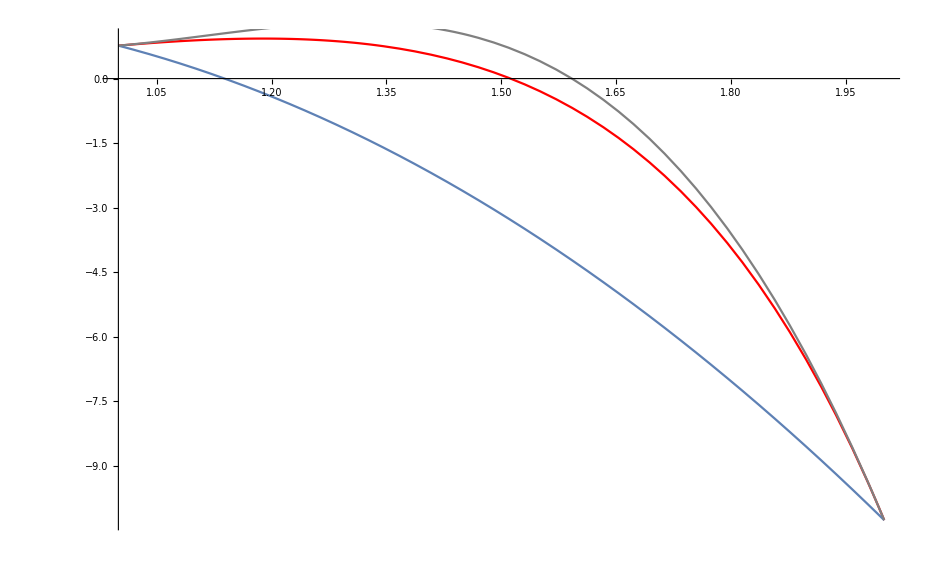

```mathematica
Show[p1,p2,p3]
```